(Z0 ω0)/(Z0 ω0+Rf (s+ω0))

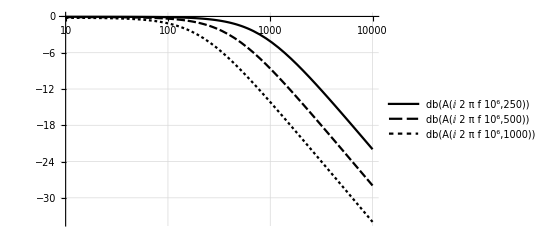

```mathematica
Z0=.;ω0=.;
A[s_,Rf_]:=(Z0/(1+s/ω0))/(Rf+Z0/(1+s/ω0));
db[a_]:=20*Log10[Abs[a]];
FullSimplify[A[s,Rf]]
Z0=40000;ω0=5000000 2π;
LogLinearPlot[{db[A[ⅈ 2π f 10^6,250]],db[A[ⅈ 2π f 10^6,500]],db[A[ⅈ 2π f 10^6,1000]]},{f,10,10000},PlotTheme->"Monochrome",GridLines->Automatic,PlotLegends->"Expressions"]
```